```mathematica
Table[ShowGraph[allGraphs5,k],{k, Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},EdgeCount[g]==7&&VertexCount[g]==5]&]}]
```

{-Graphics-29511,-Graphics-29493,-Graphics-29487,-Graphics-29485,-Graphics-29439,-Graphics-29433,-Graphics-29431,-Graphics-29415,-Graphics-29413,-Graphics-29407,-Graphics-29277,-Graphics-29271,-Graphics-29269,-Graphics-29253,-Graphics-29251,-Graphics-29245,-Graphics-29199,-Graphics-29197,-Graphics-29191,-Graphics-29173,-Graphics-28791,-Graphics-28785,-Graphics-28783,-Graphics-28767,-Graphics-28765,-Graphics-28759,-Graphics-28713,-Graphics-28711,-Graphics-28705,-Graphics-28687,-Graphics-28551,-Graphics-28549,-Graphics-28543,-Graphics-28525,-Graphics-28471,-Graphics-27333,-Graphics-27327,-Graphics-27325,-Graphics-27309,-Graphics-27307,-Graphics-27301,-Graphics-27255,-Graphics-27253,-Graphics-27247,-Graphics-27229,-Graphics-27093,-Graphics-27091,-Graphics-27085,-Graphics-27067,-Graphics-27013,-Graphics-26607,-Graphics-26605,-Graphics-26599,-Graphics-26581,-Graphics-26527,-Graphics-26365,-Graphics-22959,-Graphics-22953,-Graphics-22951,-Graphics-22935,-Graphics-22933,-Graphics-22927,-Graphics-22881,-Graphics-22879,-Graphics-22873,-Graphics-22855,-Graphics-22719,-Graphics-22717,-Graphics-22711,-Graphics-22693,-Graphics-22639,-Graphics-22233,-Graphics-22231,-Graphics-22225,-Graphics-22207,-Graphics-22153,-Graphics-21991,-Graphics-20775,-Graphics-20773,-Graphics-20767,-Graphics-20749,-Graphics-20695,-Graphics-20533,-Graphics-20047,-Graphics-9837,-Graphics-9831,-Graphics-9829,-Graphics-9813,-Graphics-9811,-Graphics-9805,-Graphics-9759,-Graphics-9757,-Graphics-9751,-Graphics-9733,-Graphics-9597,-Graphics-9595,-Graphics-9589,-Graphics-9571,-Graphics-9517,-Graphics-9111,-Graphics-9109,-Graphics-9103,-Graphics-9085,-Graphics-9031,-Graphics-8869,-Graphics-7653,-Graphics-7651,-Graphics-7645,-Graphics-7627,-Graphics-7573,-Graphics-7411,-Graphics-6925,-Graphics-3279,-Graphics-3277,-Graphics-3271,-Graphics-3253,-Graphics-3199,-Graphics-3037,-Graphics-2551,-Graphics-1093}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[Keys[allGraphs5],With[
{g=allGraphs5[#,"graph"]},
IsomorphicGraphQ[g,allGraphs5[29413,"graph"]] &&
EdgeQ[g,1<->2]&&
EdgeQ[g,1<->5]&&
EdgeQ[g,3<->2]&&
EdgeQ[g,4<->3]&&
EdgeQ[g,4<->5]
]&]}]
```

{-Graphics-29413,-Graphics-27229,-Graphics-22933,-Graphics-20773,-Graphics-20695}

```mathematica
amigo1=29413;amigo2=20773;amigo3=27229;amigo4=22933;amigo5=20695;
```

```mathematica
Table[
Table[{ShowGraph[allGraphs5,child[[1]]],ShowGraph[allGraphs5,child[[2]]]},{child,allGraphs5[a,"children"]}],
{a,amigos}]//Flatten//Tally
```

{{-Graphics-29494,2},{-Graphics-29602,1},{-Graphics-29440,1},{-Graphics-29551,1},{-Graphics-29416,2},{-Graphics-29446,1},{-Graphics-27334,1},{-Graphics-36085,1},{-Graphics-22960,2},{-Graphics-31708,1},{-Graphics-20776,2},{-Graphics-27340,1},{-Graphics-31684,1},{-Graphics-27310,1},{-Graphics-29605,1},{-Graphics-27256,2},{-Graphics-27364,1},{-Graphics-36058,1},{-Graphics-22990,1},{-Graphics-22936,1},{-Graphics-29527,1},{-Graphics-36004,1},{-Graphics-22882,1},{-Graphics-31711,1},{-Graphics-23044,1}}

```mathematica
Table[
Table[{ShowGraph[allGraphs5,child[[1]]],ShowGraph[allGraphs5,child[[2]]]},{child,allGraphs5[a,"children"]}],
{a,Flatten[allGraphs5[lambdaKey,"children"]]}]//Flatten//Tally
```

{{-Graphics-29413,2},{-Graphics-31681,2},{-Graphics-27307,2},{-Graphics-29602,2},{-Graphics-27253,2},{-Graphics-27364,2},{-Graphics-27229,2},{-Graphics-27259,2},{-Graphics-36058,2},{-Graphics-36166,2},{-Graphics-36004,2},{-Graphics-36112,2},{-Graphics-35977,2},{-Graphics-22933,2},{-Graphics-23041,2},{-Graphics-22879,2},{-Graphics-22990,2},{-Graphics-22855,2},{-Graphics-29446,2},{-Graphics-31708,2},{-Graphics-31738,2},{-Graphics-31684,2},{-Graphics-31714,2},{-Graphics-20773,2},{-Graphics-20803,2},{-Graphics-20749,2},{-Graphics-27340,2},{-Graphics-23044,2},{-Graphics-29608,2},{-Graphics-20695,2}}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[Keys[allGraphs5],With[
{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&
EdgeCount[g]==8 &&
EdgeQ[g,1<->2]&&
EdgeQ[g,1<->5]&&
EdgeQ[g,3<->2]&&
EdgeQ[g,4<->3]&&
EdgeQ[g,4<->5]
]&]}]
```

{-Graphics-29494,-Graphics-29440,-Graphics-29416,-Graphics-27334,-Graphics-27310,-Graphics-27256,-Graphics-22960,-Graphics-22936,-Graphics-22882,-Graphics-20776}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[Keys[allGraphs5],With[
{g=allGraphs5[#,"graph"]},
VertexCount[g]==3&&
EdgeCount[g]==3 
]&]}]
```

{-Graphics-29537,-Graphics-29560,-Graphics-29608,-Graphics-29633,-Graphics-29768,-Graphics-29797,-Graphics-29857,-Graphics-30262,-Graphics-30334,-Graphics-30496,-Graphics-31714,-Graphics-31738,-Graphics-31954,-Graphics-32441,-Graphics-36086,-Graphics-36112,-Graphics-36166,-Graphics-36817,-Graphics-38281,-Graphics-49208,-Graphics-49210,-Graphics-49216,-Graphics-49963,-Graphics-51475,-Graphics-56011}

```mathematica
allGraphs5[29768,"parents"]
```

{29766,29736,29676,29648,29648,29648,29648,29282,29270,29174,29037,29007,28947,27579,27549,27489,26852,26852,22721,22709,22613,9599,9587,9491,3524,3524}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,allGraphs5[29768,"parents"]}]
```

{-Graphics-29766,-Graphics-29736,-Graphics-29676,-Graphics-29648,-Graphics-29648,-Graphics-29648,-Graphics-29648,-Graphics-29282,-Graphics-29270,-Graphics-29174,-Graphics-29037,-Graphics-29007,-Graphics-28947,-Graphics-27579,-Graphics-27549,-Graphics-27489,-Graphics-26852,-Graphics-26852,-Graphics-22721,-Graphics-22709,-Graphics-22613,-Graphics-9599,-Graphics-9587,-Graphics-9491,-Graphics-3524,-Graphics-3524}

```mathematica
Table[
Table[{ShowGraph[allGraphs5,child[[1]]],ShowGraph[allGraphs5,child[[2]]]},{child,allGraphs5[a,"children"]}],
{a,Flatten[allGraphs5[lambdaKey,"children"]]}]
```

{{{-Graphics-29413,-Graphics-31681},{-Graphics-27307,-Graphics-29602},{-Graphics-27253,-Graphics-27364},{-Graphics-27229,-Graphics-27259}},{{-Graphics-36058,-Graphics-36166},{-Graphics-36004,-Graphics-36112}},{{-Graphics-29413,-Graphics-35977},{-Graphics-22933,-Graphics-23041},{-Graphics-22879,-Graphics-22990},{-Graphics-22855,-Graphics-29446}},{{-Graphics-31708,-Graphics-31738},{-Graphics-31684,-Graphics-31714}},{{-Graphics-27307,-Graphics-36058},{-Graphics-22933,-Graphics-31681},{-Graphics-20773,-Graphics-20803},{-Graphics-20749,-Graphics-27340}},{{-Graphics-29602,-Graphics-36166},{-Graphics-23044,-Graphics-29608}},{{-Graphics-27253,-Graphics-36004},{-Graphics-22879,-Graphics-31708},{-Graphics-20773,-Graphics-23041},{-Graphics-20695,-Graphics-27259}},{{-Graphics-27364,-Graphics-36112},{-Graphics-22990,-Graphics-31738}},{{-Graphics-27229,-Graphics-35977},{-Graphics-22855,-Graphics-31684},{-Graphics-20749,-Graphics-23044},{-Graphics-20695,-Graphics-20803}},{{-Graphics-29446,-Graphics-31714},{-Graphics-27340,-Graphics-29608}}}

```mathematica
Flatten[allGraphs5[lambdaKey,"children"]]
```

{27226,35977,22852,31681,20746,23041,20692,20803,20668,27259}

```mathematica
Flatten[
Table[
Table[
Table[{child[[1]]->main,child[[2]]->main},{child,allGraphs5[a,"children"]}],
{a,Flatten[allGraphs5[main,"children"]]}],
{main,{lambdaKey}}]
]
```

{29413→20665,31681→20665,27307→20665,29602→20665,27253→20665,27364→20665,27229→20665,27259→20665,36058→20665,36166→20665,36004→20665,36112→20665,29413→20665,35977→20665,22933→20665,23041→20665,22879→20665,22990→20665,22855→20665,29446→20665,31708→20665,31738→20665,31684→20665,31714→20665,27307→20665,36058→20665,22933→20665,31681→20665,20773→20665,20803→20665,20749→20665,27340→20665,29602→20665,36166→20665,23044→20665,29608→20665,27253→20665,36004→20665,22879→20665,31708→20665,20773→20665,23041→20665,20695→20665,27259→20665,27364→20665,36112→20665,22990→20665,31738→20665,27229→20665,35977→20665,22855→20665,31684→20665,20749→20665,23044→20665,20695→20665,20803→20665,29446→20665,31714→20665,27340→20665,29608→20665}

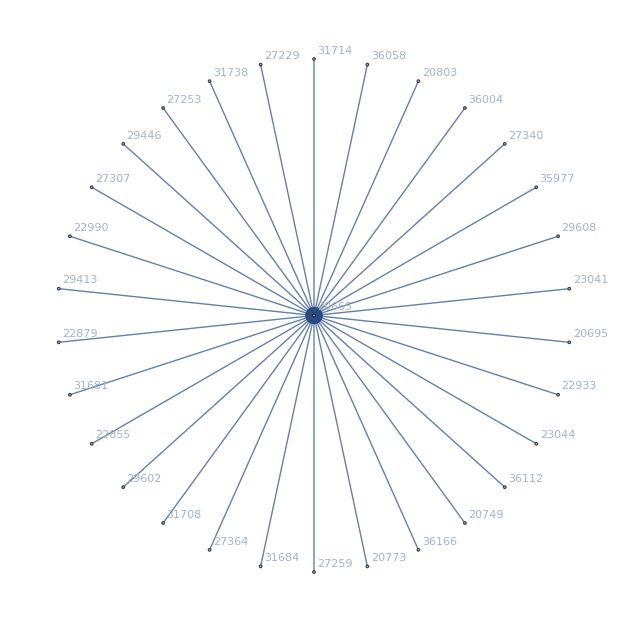

```mathematica
Graph[Flatten[
Table[
Table[
Table[{child[[1]]->main,child[[2]]->main},{child,allGraphs5[a,"children"]}],
{a,Flatten[allGraphs5[main,"children"]]}],
{main,{lambdaKey}}]
]//DeleteDuplicates,VertexLabels->Automatic,GraphLayout->"BalloonEmbedding",VertexSize->Tiny]
```

```mathematica
allGraphs5[lambdaKey,"colofour"]
```

v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5

```mathematica
PaintGraph[allGraphs5[lambdaKey,"graph"]]
```

PaintGraph[-Graphics-]

```mathematica
repFul=Table[allGraphs5[k,"colofour"]->ShowGraph[allGraphs5,k],{k,allGraphs5AtomKeys}];
```

```mathematica
repEmpty=Table[Symbol["v"<>StringDrop[SymbolName[ allGraphs5[k,"colofourrealnull"]],1]]->ShowGraph[allGraphs5,k],{k,allGraphs5NullAtomKeys}]
```

{v1x2x3x4x5→-Graphics-0,v12x3x4x5→-Graphics-39366,v123x4x5→-Graphics-52974,v1234x5→-Graphics-57528,v12345→-Graphics-59048,v1235x4→-Graphics-54492,v123x45→-Graphics-52976,v124x3x5→-Graphics-43902,v1245x3→-Graphics-45416,v124x35→-Graphics-43908,v125x3x4→-Graphics-40878,v125x34→-Graphics-40896,v12x34x5→-Graphics-39384,v12x345→-Graphics-39392,v12x35x4→-Graphics-39372,v12x3x45→-Graphics-39368,v13x2x4x5→-Graphics-13122,v134x2x5→-Graphics-17514,v1345x2→-Graphics-18980,v134x25→-Graphics-17568,v135x2x4→-Graphics-14586,v135x24→-Graphics-14748,v13x24x5→-Graphics-13284,v13x245→-Graphics-13340,v13x25x4→-Graphics-13176,v13x2x45→-Graphics-13124,v14x2x3x5→-Graphics-4374,v145x2x3→-Graphics-5834,v145x23→-Graphics-6320,v14x23x5→-Graphics-4860,v14x235→-Graphics-4920,v14x25x3→-Graphics-4428,v14x2x35→-Graphics-4380,v15x2x3x4→-Graphics-1458,v15x23x4→-Graphics-1944,v15x234→-Graphics-2124,v15x24x3→-Graphics-1620,v15x2x34→-Graphics-1476,v1x23x4x5→-Graphics-486,v1x234x5→-Graphics-666,v1x2345→-Graphics-728,v1x235x4→-Graphics-546,v1x23x45→-Graphics-488,v1x24x3x5→-Graphics-162,v1x245x3→-Graphics-218,v1x24x35→-Graphics-168,v1x25x3x4→-Graphics-54,v1x25x34→-Graphics-72,v1x2x34x5→-Graphics-18,v1x2x345→-Graphics-26,v1x2x35x4→-Graphics-6,v1x2x3x45→-Graphics-2}

```mathematica
FormulaGraph2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> ( SetsToSymbol[s]/.repFul),{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{200,200}]
]
```

```mathematica
FormulaGraph3[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> ( SetsToSymbol[s]/.repEmpty),{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{200,200}]
]
```

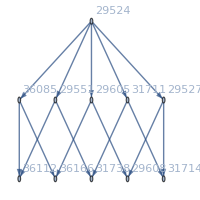

```mathematica
FormulaGraph2[allGraphs5[lambdaKey,"colofour"]]
```

```mathematica
allGraphs5[amigo1,"colofour"]
```

v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5

## Who is blocking ?

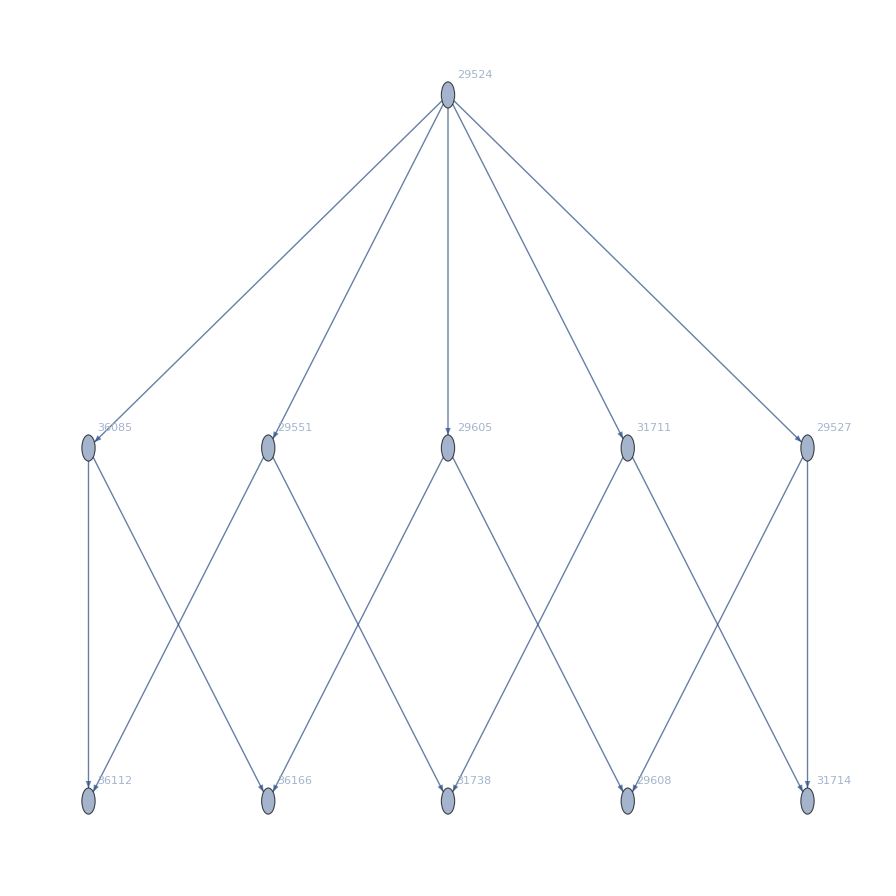
{-Graphics-20665→-Graphics-}

```mathematica
Table[
ShowGraph[allGraphs5,a]->FormulaGraph2[allGraphs5[a,"colofour"]],
{a, {lambdaKey}}
]
```

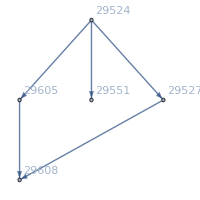
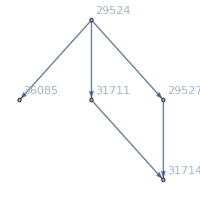
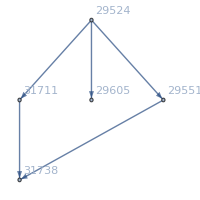
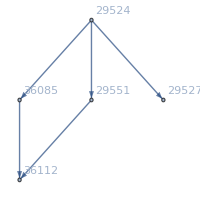
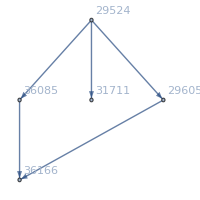
{-Graphics-29413→-Graphics-,-Graphics-20773→-Graphics-,-Graphics-27229→-Graphics-,-Graphics-22933→-Graphics-,-Graphics-20695→-Graphics-}

```mathematica
Table[
ShowGraph[allGraphs5,a]->FormulaGraph2[allGraphs5[a,"colofour"]],
{a, amigos}
]
```

```mathematica
allGraphs5[amigo1,"colofourrealnull"]
```

8 n12345-4 n1234x5-2 n1235x4-2 n123x45+2 n123x4x5-2 n1245x3+n124x3x5-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-4 n1345x2+2 n134x2x5+n135x2x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3+n14x23x5-n14x2x3x5-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5

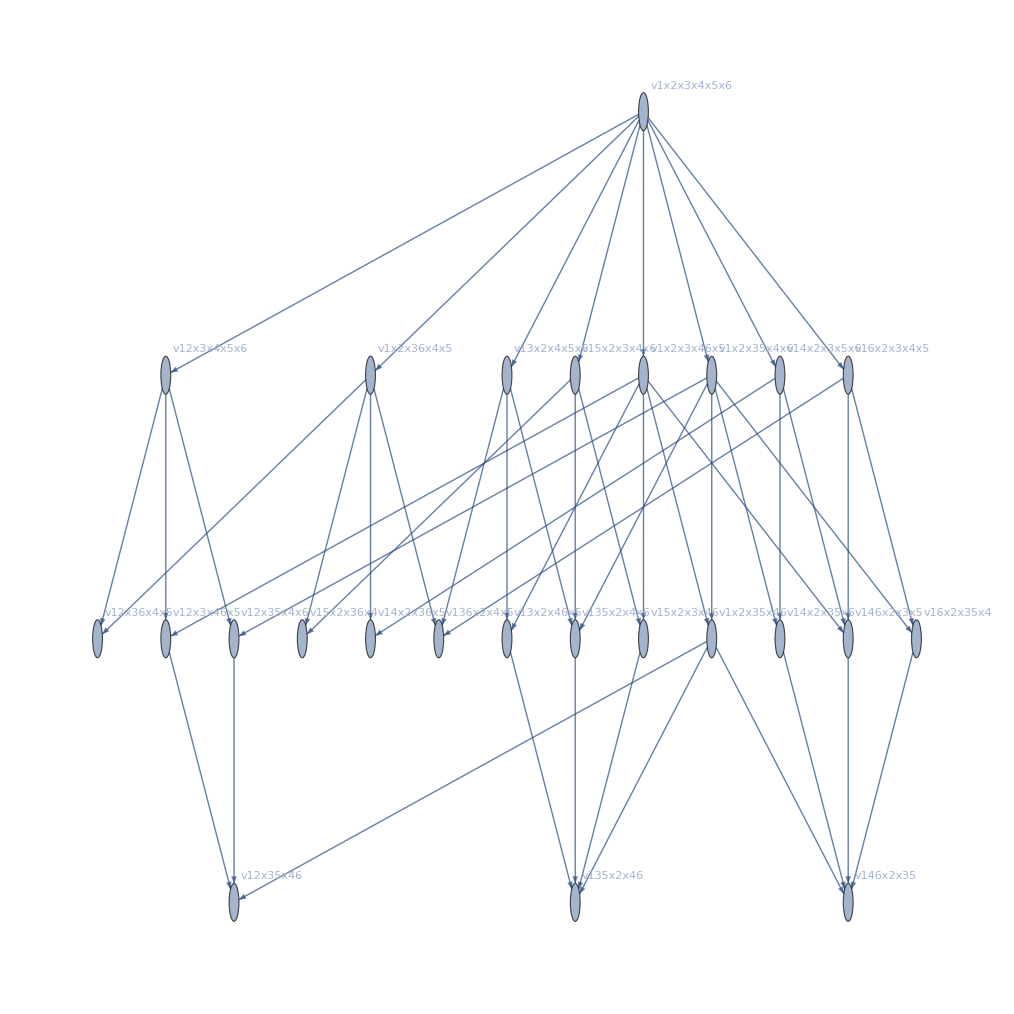
-Graphics-29413→-Graphics-

```mathematica
ShowGraph[allGraphs6,amigo1]->FormulaGraph2[allGraphs6[amigo1,"colofour"]]
```

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[Keys[allGraphs5],With[
{g=allGraphs5[#,"graph"]},
VertexCount[g]==4&&
EdgeCount[g]==6 
]&]}]
```

{-Graphics-29525,-Graphics-29527,-Graphics-29533,-Graphics-29551,-Graphics-29605,-Graphics-29767,-Graphics-30253,-Graphics-31711,-Graphics-36085,-Graphics-49207}